```mathematica
Directory[]
SetDirectory["/home/nadir/Desktop/Structural color/Mathematica works/Hydrogels"]
```

/home/nadir

/home/nadir/Desktop/Structural color/Mathematica works/Hydrogels

```mathematica
file1in=Import["fig4_sheet3_x_vs_angle.txt", "Table"]; (*angles*)
file2in=Import["fig4_sheet3_x_vs_rvalue.txt", "Table"];(*red values*)
tarray={900, 975, 1015, 1055, 1095, 1150}; (*sheet 3*)
(*tarray={32, 36, 38, 40, 42, 54};*) (*sheet 4*)
(*tarray={16, 17,18, 20, 22, 32};*) (*sheet 5*)
NN=Length[file1in];
NN2=Length[file2in];
MM=Length[tarray];
```

```mathematica
Dimensions[file2in]
```

{1420,18}

```mathematica
file1out=Table[{file1in[[ii, jj]], Cos[(90-file1in[[NN-ii+1, jj+1]])*Pi/180]}, {ii, 1, NN}, {jj, 1, 2MM, 2}];
file2out=Table[{file2in[[ii, jj+1]], file2in[[NN2-ii+1, jj+2]]}, {ii, 1, NN2}, {jj, 1, 3MM, 3}];
x2out=Table[file2in[[ii, 2]], {ii, 1, NN2}];
kk=1;
file3out=Table[{x2out[[ii]], If[x2out[[ii]]≤file1in[[kk, jj ]],  Cos[(90-file1in[[NN-kk+1, jj +1]])*Pi/180], kk++; Cos[(90-file1in[[NN-kk+1, jj+1 ]])*Pi/180]]}, {ii, 1, NN2}, {jj,1, 2MM, 2}];
```

```mathematica
ListLinePlot[file1out[[All, 3]], Filling->Axis]
```

```mathematica
redchannelfunc2[x_, nn_]:=Module[{pos, bb}, 
{bb}=Select[x2out, #≥x &, 1];
{pos}=Flatten[Position[x2out, bb]];file2out[[pos, nn, 2]]/255.];
```

```mathematica
ticksize=0.04;
tickmatrix0x={{0, 0, {ticksize, 0}, Directive[Thick, Black]}, {50, 50, {ticksize, 0},Directive[Thick, Black]} , {100, 100, {ticksize, 0},Directive[Thick, Black]},  {150, 150, {ticksize, 0},Directive[Thick, Black]}};
tickmatrix0x2={{0, "", {ticksize, 0}, Directive[Thick, Black]}, {50, "", {ticksize, 0}, Directive[Thick, Black]} , {100, "", {ticksize, 0}, Directive[Thick, Black]},  {150, "", {ticksize, 0}, Directive[Thick, Black]}};
tickmatrix0y={(*{0.85, 0.85, {ticksize, 0}, Directive[Thick, Black]},*) {0.9, 0.9, {ticksize, 0}, Directive[Thick, Black]}, {0.95, 0.95, {ticksize, 0}, Directive[Thick, Black]}};
```

```mathematica
Clear[nn];
waves=Table[{}, {mm, 1, MM}];
rmin=Min[file2out[[All, All, 2]]]/255.;
rmax=Max[file2out[[All, All, 2]]]/255.;
For[nn=1, nn≤MM, nn++, 
waves[[nn]]=ListLinePlot[file3out[[All, nn]], Filling->Axis, PlotStyle->Directive[Thick],AxesStyle->{{Black, Thick}, {Black, Thick}},  Ticks->{If[nn==MM, tickmatrix0x, tickmatrix0x2], tickmatrix0y},  BaseStyle->{FontSize->28},TicksStyle->Directive[Thick, Black], ColorFunction->Function[{x, y}, RGBColor[(redchannelfunc2[x, nn]-rmin)/(rmax-rmin), 0.44+(redchannelfunc2[x, nn]-rmin) (0.87-0.44)/(rmax-rmin),0.75+(redchannelfunc2[x, nn]-rmin) (0.48-0.75)/(rmax-rmin)]],  ColorFunctionScaling->False, PlotRange->{{0, Max[x2out]}, {0.85, 0.98}}, AspectRatio->1/6  (*AxesLabel->{If[nn==6, "x(μm)", ""], If[nn==3, "h/H", ""]}*)];]
```

```mathematica
Show[waves, PlotRange->{{0, 160}, {0.9, 0.95}}]
```

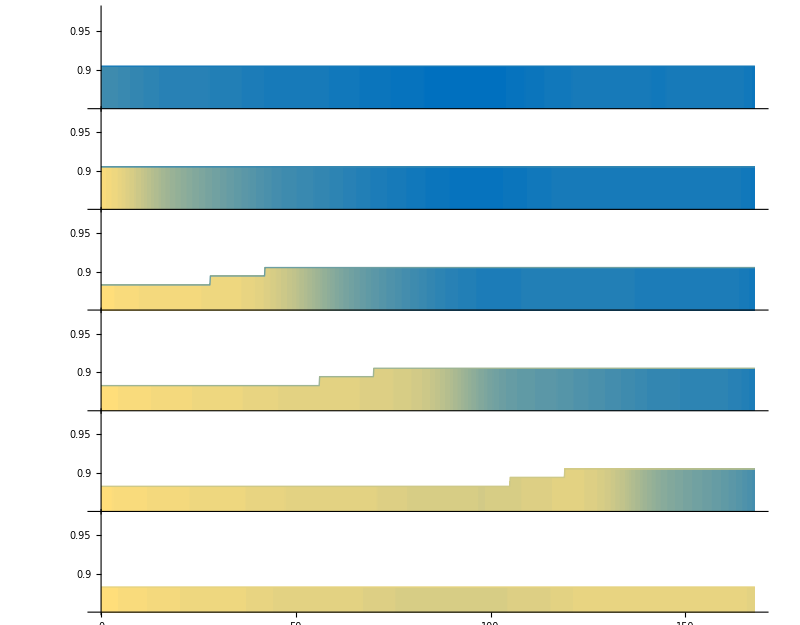

```mathematica
gridcol=GraphicsColumn[waves, ImageSize->{800, 750*5/6}, Spacings->Scaled[-0.2]]
```

```mathematica
nn
```

7

```mathematica
Dimensions[file2out]
```

{1420,6,2}

```mathematica
Dimensions[file3out]
```

{1420,6,2}

```mathematica
{aa}=Select[x2out, #>0 &, 1]
```

{0.117978}

```mathematica
Flatten[Position[x2out, aa]]
```

{2}

```mathematica
file1out[[2, 1]][[1]]
```

7

```mathematica
file1out[[1, 1]][[1]]
```

0

```mathematica
Dimensions[file1out]
```

{25,6,2}